```mathematica
(*For every terminating continued fraction x, there is an associated element of SL(2,\mathbb{Z})
by T^{b_1}ST^{-b_2}ST^{b_3}S\cdotsT^{b_max}S
It has the property that it's action on \infty gives back x
*)
```

```mathematica
ModularS:={{0,1},{-1,0}};
ModularT:={{1,1},{0,1}};
RationalFracToModular[x_,maxDepth_]:=Module[{contFrac,intPart,i,length,returnVal},
returnVal=IdentityMatrix[2];
contFrac=ContinuedFraction[x,maxDepth];
intPart=contFrac[[1]];
(*Print[intPart];*)
contFrac=Rest[contFrac];
(*Print[contFrac];*)
length=Length[contFrac];
For[i=1,i<=length,i++,
returnVal=returnVal.(MatrixPower[ModularT,(-1)^i*contFrac[[i]]]);
returnVal=returnVal.ModularS;
];
returnVal=MatrixPower[ModularT,intPart].ModularS.returnVal
]
```

```mathematica
x=Pi^3*E;
result=RationalFracToModular[x,10];
result//MatrixForm
N[x]
x=result[[1]][[1]]/result[[2]][[1]];
N[x]
```

(-16133099 | -3180112
-191414 | -37731)

84.2838

84.2838

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 15 terms.

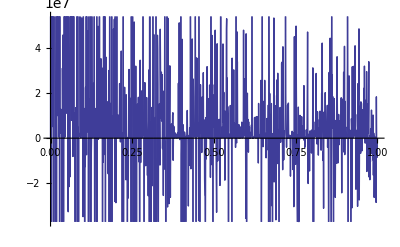

```mathematica
(*The matrix elements of the associated element of the modular group are messily dependent on the input rational number*)
Plot[RationalFracToModular[x,15][[2]][[1]],{x,0,1},PlotPoints->20]
```